# Linear Regression

Whenever we perform a linear regression on some data, we might get carried away by good values of R^2 or p. However, such single valued quantities don’t tell the whole story.

## Temperature Model

We will create a model that is a function of temperature:

```mathematica
c = RandomReal[{0,25}];
y = RandomReal[{0,100}];
M[T_]:= c T + y;
```

We will now add random noise to the model:

```mathematica
Nsamples = 250;
Tsamples = RandomReal[{0,100}, Nsamples]//Sort;
noise = 25;
Msamples = (M/@Tsamples)+RandomVariate[NormalDistribution[0,noise c],Nsamples];
```

```mathematica
MTdata = Riffle[Tsamples, Msamples] //Partition[#,2]&;
```

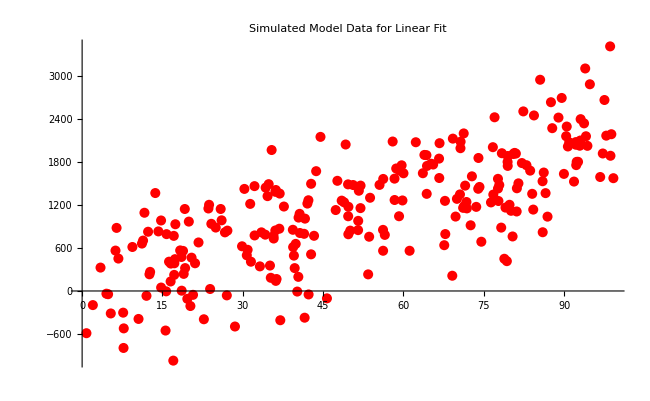

```mathematica
ListPlot[MTdata,PlotLabel->"Simulated Model Data for Linear Fit", ImageSize->650, PlotStyle->Red]
```

## Linear Fit of the Data

We will use the Mathematica’s built-in fitting to do a standard linear-regression:

```mathematica
lm = LinearModelFit[MTdata,x,x];
```

```mathematica
{py,pc} = CoefficientList[Normal[lm],x]
```

{63.5461,8.52401}

```mathematica
Abs[py-y]
Abs[pc-c]
```

17.8409

0.566689

```mathematica
Sqrt[Plus@@Abs[(lm/@Tsamples)-Msamples]/Nsamples]
```

20.4978

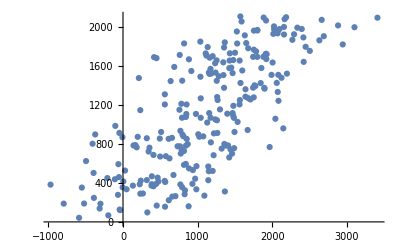

```mathematica
ListPlot[Riffle[Msamples,(lm/@Tsamples)]//Partition[#,2]&]
```

## Residuals vs Fitted Values

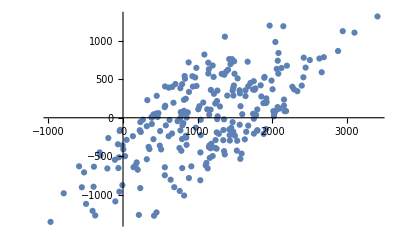

```mathematica
fvals = lm/@Tsamples;
res = Msamples-fvals;
ListPlot[Transpose[{Msamples,res}]]
```

```mathematica
lm["FitResiduals"]-res
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

So the lm[“FitResiduals”] does the same thing as our function above that found the residuals.

## Quantile Plots

```mathematica
Msamples
```

{-79.1778,270.527,196.501,383.861,513.393,42.3732,176.829,-169.238,311.778,309.698,10.109,225.056,5.08744,122.083,-56.7882,-66.3755,-53.0647,139.82,34.7369,382.467,213.764,340.885,165.873,49.2139,46.841,44.067,108.928,-104.022,574.78,511.884,-205.467,-86.4605,277.937,473.29,448.986,426.134,694.811,364.762,235.298,246.213,154.505,68.7574,61.4833,300.483,266.701,233.948,376.869,175.487,427.539,87.6686,273.541,371.579,387.108,257.802,33.3296,-273.413,350.733,-20.6731,350.834,383.036,-66.0876,21.8541,163.174,147.65,222.994,346.855,543.713,72.0556,721.673,447.303,482.739,523.758,596.022,214.072,587.176,8.20119,499.036,57.0369,126.134,560.145,82.5231,-42.8571,338.563,575.688,255.257,497.89,397.169,323.949,304.894,628.549,737.823,41.2698,57.652,-48.7028,477.411,147.134,448.609,313.448,237.872,575.203,270.732,789.965,371.919,160.479,775.847,100.363,242.233,465.281,255.989,344.78,300.744,661.128,741.049,622.824,348.724,198.367,355.96,362.171,521.402,754.1,255.524,292.711,563.823,616.171,71.1998,373.503,289.188,413.966,429.168,246.295,754.455,430.702,736.9,726.256,342.609,888.31,678.392,480.293,366.9,457.252,796.67,359.518,950.33,582.94,541.066,299.007,624.977,556.276,314.475,645.92,254.9,826.828,269.851,904.1,760.407,603.569,1077.92,544.979,569.573,769.081,307.182,175.521,104.786,204.098,576.655,412.85,518.278,491.998,512.211,747.434,475.629,964.751,818.842,763.565,1285.83,487.754,657.239,864.728,611.438,851.36,501.331,644.555,539.338,673.565,723.69,348.561,558.114,1208.35,289.769,751.854,246.156,819.313,560.874,1038.81,431.507,1203.01,589.908,705.851,904.383,801.775,422.716,831.992,1036.7,415.981,508.886,655.725,893.322,423.426,689.623,787.636,944.105,1050.02,1075.21,626.817,665.71,549.299,980.685,788.009,721.479,913.52,982.704,1086.44,1202.43,804.378,1069.23,980.781,500.193,853.887,1077.72,700.443,327.598,882.489,632.873,1122.72,592.743,902.157,837.643,1230.12,784.89,756.088,745.287,1003.85,942.119,1437.91,400.614,1032.27,839.267,1140.62,955.61,1181.49}

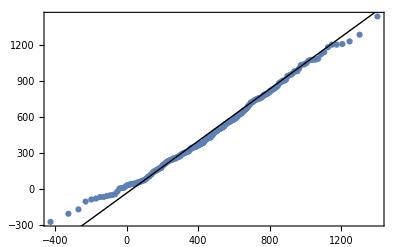

```mathematica
QuantilePlot[Msamples]
```

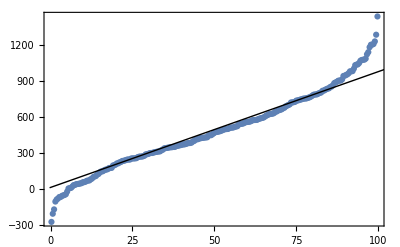

```mathematica
QuantilePlot[Msamples,UniformDistribution[{0,100}]]
```

## Spread - Location Plot

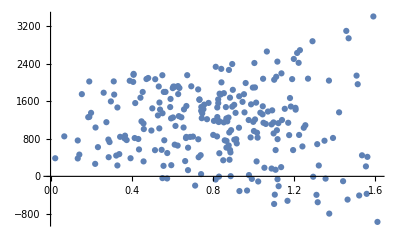

```mathematica
ListPlot[Riffle[Sqrt[Abs[lm["StandardizedResiduals"]]],Msamples]//Partition[#,2]&]
```

## Residuals vs Leverage

```mathematica
influence = Riffle[lm["HatDiagonal"],lm["StandardizedResiduals"]]//Partition[#,2]&;
cooks = Riffle[lm["CookDistances"],lm["StandardizedResiduals"]]//Partition[#,2]&;
```

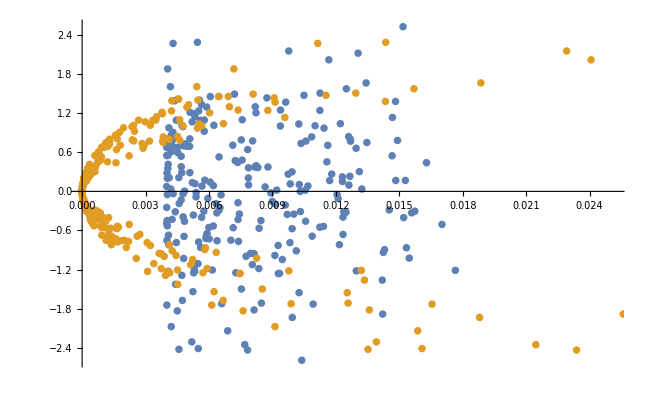

```mathematica
ListPlot[{influence,cooks},ImageSize->650]
```